```mathematica
SetDirectory[NotebookDirectory[]];
```

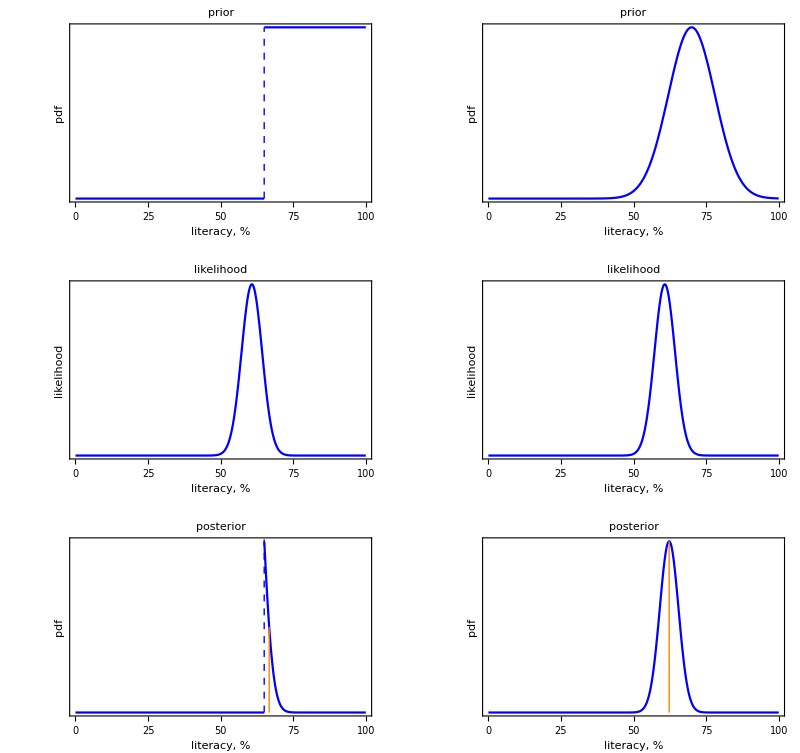

```mathematica
aCutoff = 65;
vData = {60,66,60,60,60,60,60,60};
aPrior = UniformDistribution[{aCutoff,100}];
aLikelihood = NormalDistribution[μ,10];
g1=Plot[PDF[aPrior,x],{x,0,100},Frame->{True,True,False,False},FrameLabel->{"literacy, %","pdf"},FrameTicks->{Automatic,None},PlotStyle->Blue,BaseStyle->{FontSize->14},Epilog->{Dashed,Blue,Line[{{aCutoff,0},{aCutoff,1/(100-aCutoff)}}]},PlotLabel->"prior"];
g2=Plot[Likelihood[aLikelihood,vData],{μ,0,100},Frame->{True,True,False,False},FrameLabel->{"literacy, %","likelihood"},FrameTicks->{Automatic,None},PlotStyle->Blue,BaseStyle->{FontSize->14},PlotLabel->"likelihood",PlotRange->Full];
aPost = (PDF[aPrior,μ] Likelihood[aLikelihood,vData]);
aInt = NIntegrate[PDF[aPrior,μ] Likelihood[aLikelihood,vData],{μ,0,100}];
aMean= (1/aInt)NIntegrate[μ PDF[aPrior,μ] Likelihood[aLikelihood,vData],{μ,0,100}];
g3 = Plot[aPost,{μ,0,100},Frame->{True,True,False,False},FrameLabel->{"literacy, %","pdf"},FrameTicks->{Automatic,None},PlotStyle->Blue,BaseStyle->{FontSize->14},PlotRange->Full,Epilog->{{Dashed,Blue,Line[{{aCutoff,0},{aCutoff,aPost/.{μ->aCutoff}}}]},{Thick,Orange,Line[{{aMean,0},{aMean,aPost/.{μ->aMean}}}]}},PlotLabel->"posterior"];
aPrior2 = NormalDistribution[70,8];
g4=Plot[PDF[aPrior2,x],{x,0,100},Frame->{True,True,False,False},FrameLabel->{"literacy, %","pdf"},FrameTicks->{Automatic,None},PlotStyle->Blue,BaseStyle->{FontSize->14},PlotLabel->"prior",PlotRange->Full];
g5=Plot[Likelihood[aLikelihood,vData],{μ,0,100},Frame->{True,True,False,False},FrameLabel->{"literacy, %","likelihood"},FrameTicks->{Automatic,None},PlotStyle->Blue,BaseStyle->{FontSize->14},PlotLabel->"likelihood",PlotRange->Full];
aPost2 = (PDF[aPrior2 ,μ] Likelihood[aLikelihood,vData]);
aInt2 = NIntegrate[PDF[aPrior2,μ] Likelihood[aLikelihood,vData],{μ,0,100}];
aMean2 = (1/aInt2)NIntegrate[μ PDF[aPrior2,μ] Likelihood[aLikelihood,vData],{μ,0,100}];
g6 = Plot[aPost2,{μ,0,100},Frame->{True,True,False,False},FrameLabel->{"literacy, %","pdf"},FrameTicks->{Automatic,None},PlotStyle->Blue,BaseStyle->{FontSize->14},PlotRange->Full,Epilog->{Thick,Orange,Line[{{aMean2,0},{aMean2,aPost2/.{μ->aMean2}}}]},PlotLabel->"posterior"];
gFinal=Show[GraphicsGrid[{{g1,g4},{g2,g5},{g3,g6}}],ImageSize->800]
```

```mathematica
Export["Prior_overZealous.pdf",gFinal]
```

Prior_overZealous.pdf